```mathematica
Quit[];
```

```mathematica
ScalarF0[m_,s_]:=If[s==0,-2Log[m],If[s==4 m^2,2-2Log[m],2-2Log[m]-(2 √(4 m^2-s))/(√s)ArcTan[(√s)/(√(4 m^2-s))]]] ;
ScalarFPrime0[m_,s_]:=If[s==4 m^2,-1/(4 m^2),-1/s+(4 m^2)/(√(4 m^2-s) s^(3/2))ArcTan[(√s)/(√(4 m^2-s))]];
PropagatorScalar[s_,M_,m_,c_,Γ_]:=1/(s-M^2+ⅈ×M×Γ+c×(ScalarF0[m,s]-ScalarF0[m,M^2]-(s-M^2)Re[ScalarFPrime0[m,M^2]]));
```

```mathematica
NWA[p_,A_,B_,C_]:=C/((p^2-A)^2+B);
```

```mathematica
BestFit[M_,m_,c_,Γ_]:=FindMinimum[Sum[(Abs[PropagatorScalar[p^2,M,m,c,Γ]]^2-NWA[p,A,B,C])^2,{p,M-4Γ,M+4Γ,0.1Γ}],{{A,M^2},{B,M^2 Γ^2},{C,1}},MaxIterations->Infinity,AccuracyGoal->20,PrecisionGoal->18,WorkingPrecision->MachinePrecision];
```

```mathematica
DiffSectionRatio[M_,m_,c_,Γ_,Ein_]:=(
Res=BestFit[M,m,c,Γ];
TotalSection=NIntegrate[Abs[PropagatorScalar[p^2,M,m,c,Γ]]^2,{p,M-4Γ,M+4Γ},MaxRecursion->20,WorkingPrecision->MachinePrecision];
DiffTotalSection=NIntegrate[Abs[Abs[PropagatorScalar[p^2,M,m,c,Γ]]^2-(NWA[p,A,B,C]/.Res[[2]])],{p,M-4Γ,M+4Γ},MaxRecursion->10,WorkingPrecision->MachinePrecision];
DiffTotalSection/TotalSection
)
```

```mathematica
NWATotalCross1=(EE^2 M ylsq^2(Ein^2-M^2)(-2 M^2 Ein^2+2(M^4+Ein^4)ArcTanh[√(1-(4 Subscript[m, e]^2)/Ein^2)]))/(32 π^2 Γ Ein^4(Ein^2-M^2)^2);
```

```mathematica
16 π^2 c √Max[1-(4 m^2)/M^2,0]+ylsq×M^2≤16π M Γ
cmax=(M Γ)/π (Max[1-(4 m^2)/M^2,0])^(-1/2);
ylsqmax=(16π Γ)/M-(16 π^2 c)/M^2 √Max[1-(4 m^2)/M^2,0];
```

16 π^2 c √(max(0,1-(4 m^2)/M^2))+M^2 ylsq≤16 π Γ M

```mathematica
PercentagePlot[M_?NumericQ,Γ_?NumericQ,Ein_?NumericQ]:=Show[DensityPlot[Quiet[DiffSectionRatio[M,m,c,Γ,Ein],{NIntegrate::slwcon}],{m,M/2-Γ,M/2+Γ},{c,M^2/(4π×100),M^2/(4π)},PlotLegends->Automatic,PlotRange->Full],
RegionPlot[16 π^2 c √Max[1-(4 m^2)/M^2,0]≥16π M Γ||(Re[ScalarFPrime0[m,M^2]]-1/(6 m^2))c>1,{m,M/2-Γ,M/2+Γ},{c,M^2/(4π×100),M^2/(4π)},BoundaryStyle->None,PlotStyle->White,MaxRecursion->10]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 10 recursive bisections in p near {p} = {380.078}. NIntegrate obtained 3.29627×10^-10 and 2.36483×10^-15 for the integral and error estimates.

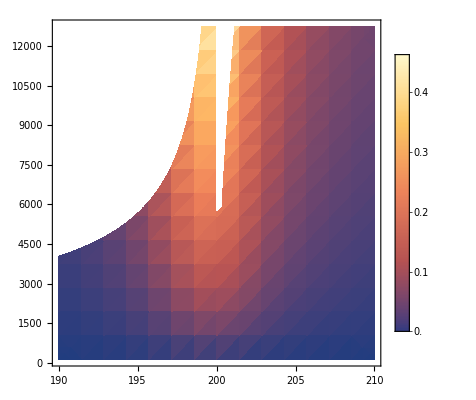

```mathematica
PercentagePlot[400,10,500]
```